MAJ3

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

4+4 p+7 p^2+6 p^3-57 p^4+20 p^5+68 p^6-64 p^7+16 p^8

4+4 p+6 p^2+9 p^3-61 p^4+23 p^5+67 p^6-64 p^7+16 p^8

6.1875

6.14063

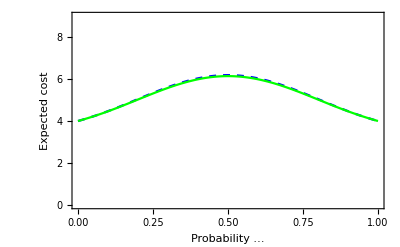

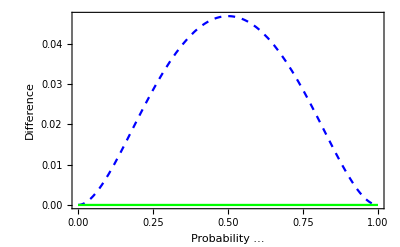

```mathematica
A4hs[p_]=4p^0+4p^1+7p^2+6p^3+-57p^4+20p^5+68p^6+-64p^7+16p^8+0p^9
A[p_]= 4p^0+4p^1+6p^2+9p^3+-61p^4+23p^5+67p^6+-64p^7+16p^8
N[A4hs[1/2]]
N[A[1/2]]

plot = Plot[{A4hs[p],A[p]},{p,0,1},PlotLegends->{MaTeX@{"P_t(p)","P_*(p)"}}, Frame -> True,FrameLabel->{StringForm["Probability ``",MaTeX["p"]], "Expected cost"},LabelStyle->{Black,Medium},PlotRange->{{0,1},{0,9}},PlotStyle->{{Dashed, Blue},Green}]
diffplot = Plot[{A4hs[p]-A[p],A[p]-A[p]},{p,0,1},PlotLegends->{MaTeX@{"P_t(p)-P_*(p)"}},Frame -> True,FrameLabel->{StringForm["Probability ``",MaTeX["p"]], "Difference"},LabelStyle->{Black,Medium} ,PlotRange->Full,PlotStyle->{{Dashed, Blue},Green}]
plotDp = Show[plotDp,Epilog->{PointSize->Large,Point[{{0.5,6.1875}}]}]
```

```mathematica
Export["/home/julia/git/LevelpComplexityOfBooleanFunctions/paper/plots/itermajalgsdiff2.pdf",diffplot,"PDF"]
```

/home/julia/git/LevelpComplexityOfBooleanFunctions/paper/plots/itermajalgsdiff2.pdf

```mathematica
Export["/home/julia/git/LevelpComplexityOfBooleanFunctions/paper/plots/itermajalgs2.pdf",plot,"PDF"]
```

/home/julia/git/LevelpComplexityOfBooleanFunctions/paper/plots/itermajalgs2.pdf